```mathematica
2 + 3
```

5

```mathematica
ClearAll["Global`*"]
C=3.*^6;   
T=16.*^-6;    
plist={4096,1024,512,48};   
acquisitionProb[Q_?NumericQ]:=If[Q==1,1.,(1-1./Q)^(Q-1)];
waitSlots[Q_?NumericQ]:=(1-acquisitionProb[Q])/acquisitionProb[Q];
efficiency[P_?NumericQ,Q_?NumericQ]:=Module[{W=waitSlots[Q]},(P/C)/((P/C)+W*T)];
fmt[x_]:=NumberForm[x,{4,2}];  
table=Grid[Prepend[Table[With[{Q=q},Prepend[fmt/@(100*efficiency[#,Q]&/@plist),Q]   (*%*)],{q,{1,2,3,4,5,10,32,64,128,256}}],Prepend[plist,"Q \\ P (bits)"]],Frame->All,Alignment->Center]
```

Set::wrsym: Symbol C is Protected.

Q \ P (bits) | 4096 | 1024 | 512 | 48
1 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
2 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
3 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
4 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
5 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
10 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
32 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
64 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
128 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)
256 | 409600/((0.00+4096/C) C) | 102400/((0.00+1024/C) C) | 51200/((0.00+512/C) C) | 4800/((0.00+48/C) C)

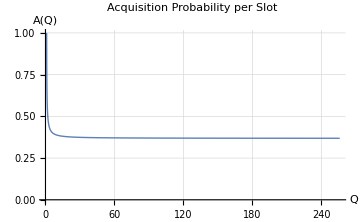

```mathematica
acquisitionProb[Q_?NumericQ]:=If[Q==1,1.,(1-1./Q)^(Q-1)];
acqPlot=Plot[acquisitionProb[q],{q,1,256},AxesLabel->{"Q","A(Q)"},PlotRange->{0,1},ImageSize->Medium,PlotLabel->"Acquisition Probability per Slot",GridLines->Automatic,PlotStyle->Thick];
acqPlot
```

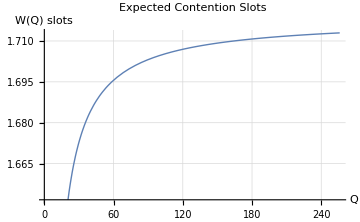

```mathematica
waitSlots[Q_?NumericQ]:=(1-acquisitionProb[Q])/acquisitionProb[Q];
waitPlot=Plot[waitSlots[q],{q,1,256},AxesLabel->{"Q","W(Q) slots"},ImageSize->Medium,PlotLabel->"Expected Contention Slots",GridLines->Automatic,PlotStyle->Thick];
waitPlot
```

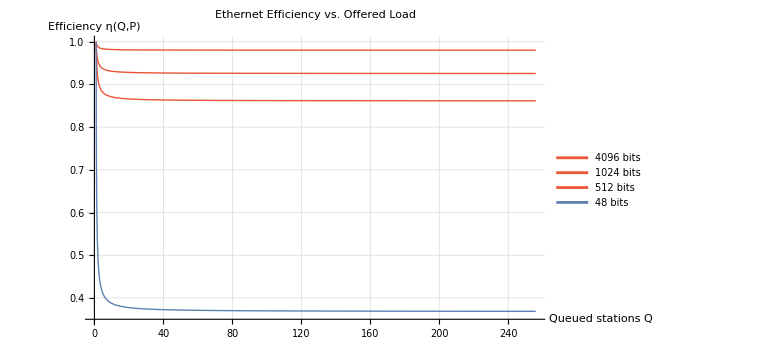

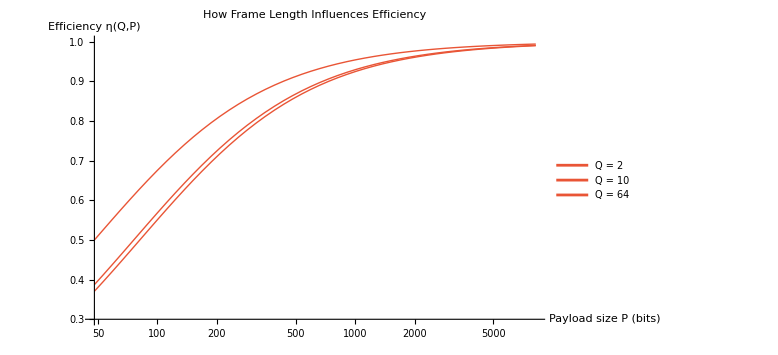

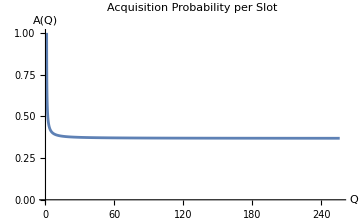

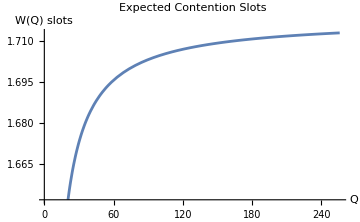

```mathematica
ClearAll["Global`*"];
channelRate=3.*^6; 
slotTime=16.*^-6;
acquisitionProb[Q_?NumericQ]:=If[Q==1,1.,(1-1./Q)^(Q-1)];
waitSlots[Q_?NumericQ]:=(1-acquisitionProb[Q])/acquisitionProb[Q];
efficiency[P_?NumericQ,Q_?NumericQ]:=Module[{W=waitSlots[Q]},(P/channelRate)/((P/channelRate)+W*slotTime)]
throughput[P_,Q_]:=channelRate*efficiency[P,Q];  
payloads={4096,1024,512,48}; 
palette=ColorData[97]/@Rescale[Range[Length[payloads]]];
effPlot=Plot[Evaluate@Table[efficiency[p,q],{p,payloads}],{q,1,256},PlotStyle->Thread[{palette,Thick}],PlotLegends->(ToString[#]<>" bits"&/@payloads),AxesLabel->{"Queued stations  Q","Efficiency  η(Q,P)"},PlotRange->{0.35,1},GridLines->Automatic,ImageSize->Large,PlotLabel->"Ethernet Efficiency vs. Offered Load"];
effPlot
qs={2,10,64}; 
effPlot2=LogLinearPlot[Evaluate@Table[efficiency[p,q],{q,qs}],{p,48,8192},PlotStyle->Thread[{palette[[;;Length[qs]]],Thick}],PlotLegends->(Style["Q = "<>ToString[#],Bold]&/@qs),AxesLabel->{"Payload size  P (bits)","Efficiency  η(Q,P)"},PlotRange->{0.3,1},ImageSize->Large,PlotLabel->"How Frame Length Influences Efficiency"];
effPlot2
acqPlot=Plot[acquisitionProb[q],{q,1,256},AxesLabel->{"Q","A(Q)"},PlotRange->{0,1},ImageSize->Medium,PlotLabel->"Acquisition Probability per Slot"];
acqPlot
waitPlot=Plot[waitSlots[q],{q,1,256},AxesLabel->{"Q","W(Q) slots"},ImageSize->Medium,PlotLabel->"Expected Contention Slots"];
waitPlot
```

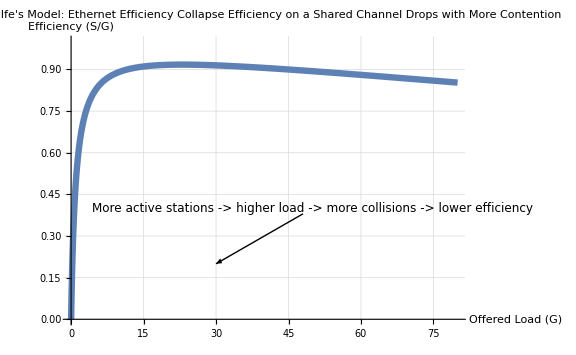

```mathematica
packetSize=1500*8;
bandwidth=10*^6;
propSpeed=2.3*^8; 
linkDistance=500; 
jamSize=32; 
packetTime=packetSize/bandwidth;
propDelay=linkDistance/propSpeed;
a=propDelay/packetTime; 
efficiency[G_]:=(G*Exp[-a*G])/(G*(1+2 a)+Exp[-a*G]);
Plot[efficiency[G],{G,0,80},PlotRange->{0,1},AxesLabel->{"Offered Load (G)","Efficiency (S/G)"},PlotLabel->Column[{Style["Metcalfe's Model: Ethernet Efficiency Collapse",16,Bold],Style["Efficiency on a Shared Channel Drops with More Contention",12]},Alignment->Center],PlotStyle->{Thickness[0.008],ColorData[97,1]},GridLines->Automatic,ImageSize->Large,Epilog->{Text[Style["More active stations -> higher load -> more collisions -> lower efficiency",12],{50,0.4}],Arrow[{{48,0.38},{30,0.2}}]}]
```

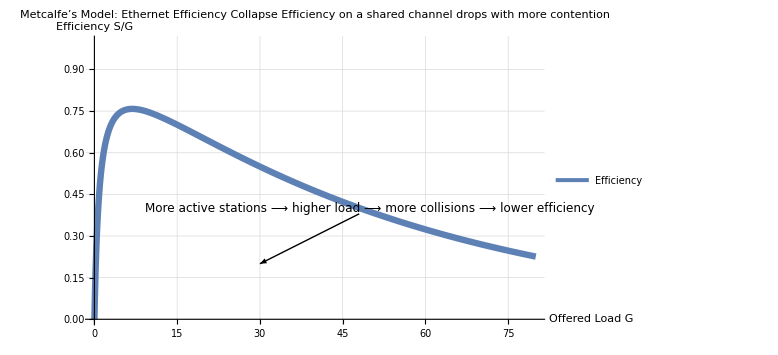

```mathematica
ClearAll["Global`*"];
packetSize=15*8;     
bandwidth=10^6;        
propSpeed=2.3*^8;  
linkDistance=500;        
jamSize=32;   
packetTime=packetSize/bandwidth;
propDelay=linkDistance/propSpeed;
jamTime=jamSize/bandwidth;
a=propDelay/packetTime;  
efficiency[G_]:=(G Exp[-a G])/(G (1+2 a)+Exp[-a G]);
effPlot=Plot[efficiency[G],{G,0,80},PlotRange->{0,1},AxesLabel->(Style[#,12]&/@{"Offered Load  G","Efficiency  S/G"}),PlotStyle->{Thickness[.008],ColorData[97,1]},GridLines->Automatic,ImageSize->Large,PlotLegends->Placed[{"Efficiency"},{0.8,.9}],PlotLabel->Style[Row[{"Metcalfe’s Model: Ethernet Efficiency Collapse\n",Style["Efficiency on a shared channel drops with more contention",12,Gray]}],16,Bold],Epilog->{Inset[Style["More active stations ⟶ higher load ⟶ more collisions ⟶ lower efficiency",12],{50,.4}],Arrow[{{48,.38},{30,.2}}]}];
effPlot
```

```mathematica
Manipulate[Module[{packetTime,propDelay,a,efficiency},packetTime=packetSizeBytes*8/(bandwidthGbit*1*^9);
propDelay=linkDistMeters/(2.3*^8);
a=propDelay/packetTime;
efficiency=1/(1+2 a);
Plot[1/(1+2 (d/(2.3*^8))/(packetSizeBytes*8/(bandwidthGbit*1*^9))),{d,0,500},PlotRange->{0,1.05},AxesLabel->{"Link Distance (meters)","Link Utilization (Efficiency)"},PlotLabel->Column[{Style["Point-to-Point Link Efficiency",16,Bold],Style["Efficiency vs. Distance for a Given Bandwidth and Packet Size",12]},Alignment->Center],PlotStyle->{Thickness[0.008],ColorData[97,2]},GridLines->Automatic,ImageSize->Large,Epilog->{Dashed,Line[{{linkDistMeters,-1},{linkDistMeters,efficiency}}],Line[{{-100,efficiency},{linkDistMeters,efficiency}}],PointSize[Large],Point[{linkDistMeters,efficiency}],Text[Style["Efficiency at "<>ToString[linkDistMeters]<>"m: "<>ToString[PaddedForm[efficiency*100,{3,2}]]<>"%",14,Black,Background->White],{250,0.4}]}]],{{packetSizeBytes,1500,"Packet Size (Bytes)"},64,8000,Appearance->"Labeled"},{{bandwidthGbit,10,"Bandwidth (Gbps)"},1,100,Appearance->"Labeled"},{{linkDistMeters,10,"Link Distance (m)"},0.1,500,Appearance->"Labeled"},ControlPlacement->Left]
```

Set::wrsym: Symbol C is Protected.

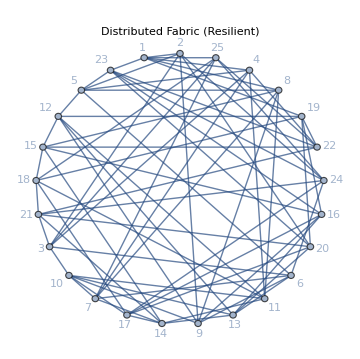

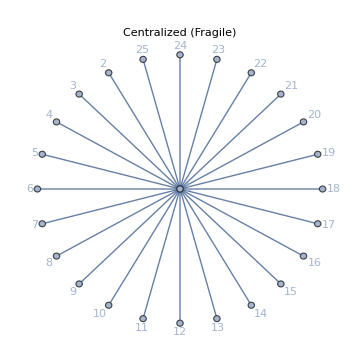
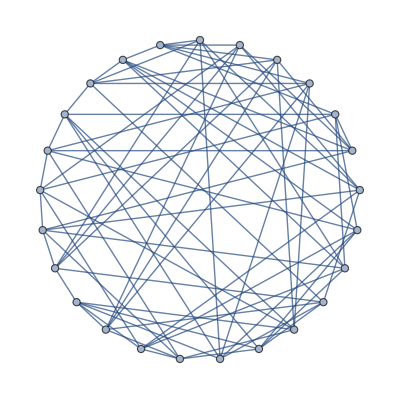

Resilience of Centralized Network:

Resilience of Distributed Fabric:

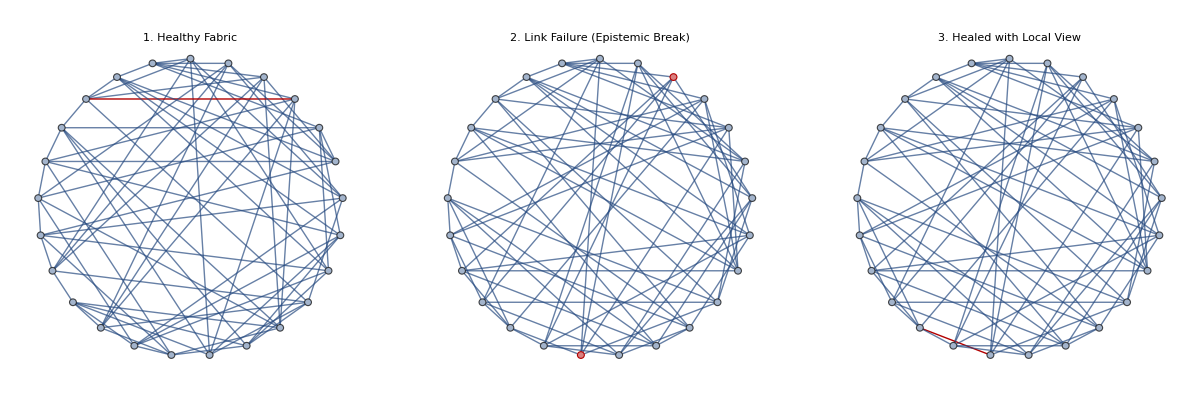

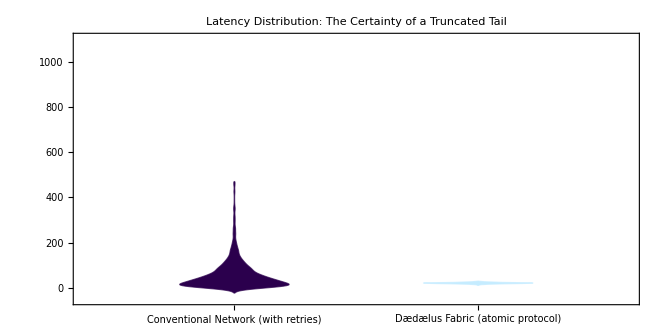

```mathematica
MSS=1500; 
C=1.22; 
mathisThroughput[RTT_?NumericQ,p_?NumericQ]:=(MSS/RTT)*(C/Sqrt[p]);
centralizedNetwork=StarGraph[25,ImageSize->Medium,VertexLabels->"Name",PlotLabel->"Centralized (Fragile)"];
distributedFabric=EdgeAdd[CycleGraph[25],Flatten[Table[{i<->Mod[i+3,25,1],i<->Mod[i+7,25,1]},{i,1,25}]]];
SetProperty[distributedFabric,{ImageSize->Medium,VertexLabels->"Name",PlotLabel->"Distributed Fabric (Resilient)"}]
Row[{centralizedNetwork,distributedFabric},Spacer[20]]
calculateResilienceMetrics[graph_Graph]:=<|"Vertex Connectivity"->VertexConnectivity[graph],"Edge Connectivity"->EdgeConnectivity[graph]|>;
Print["Resilience of Centralized Network:"];
calculateResilienceMetrics[centralizedNetwork]//Dataset
Print["Resilience of Distributed Fabric:"];
calculateResilienceMetrics[distributedFabric]//Dataset
simulateLinkFailure[graph_Graph,edge_]:=EdgeDelete[graph,edge];
localHealingProtocol[graph_Graph,{node1_,node2_}]:=Module[{neighbors1,neighbors2,sharedNeighbors,newPath},neighbors1=AdjacencyList[graph,node1];
neighbors2=AdjacencyList[graph,node2];
sharedNeighbors=Intersection[neighbors1,neighbors2];
If[Length[sharedNeighbors]>0,newPath={node1<->First[sharedNeighbors],First[sharedNeighbors]<->node2};
EdgeAdd[graph,newPath],graph]];
failedEdge=5<->8;
brokenFabric=simulateLinkFailure[distributedFabric,failedEdge];
healedFabric=localHealingProtocol[brokenFabric,{5,8}];
GraphicsRow[{HighlightGraph[distributedFabric,failedEdge,GraphHighlightStyle->"Thick",PlotLabel->"1. Healthy Fabric"],HighlightGraph[brokenFabric,{5,8},GraphHighlightStyle->"Dashed",PlotLabel->"2. Link Failure (Epistemic Break)"],HighlightGraph[healedFabric,{5<->12,12<->8},PlotLabel->"3. Healed with Local View"]},ImageSize->Full]
conventionalLatency:=RandomVariate[ExponentialDistribution[1/50]]+If[RandomReal[]<0.1,RandomVariate[ExponentialDistribution[1/200]],0];
daedalusLatency:=RandomVariate[NormalDistribution[20,3]];
latencies=<|"Conventional Network (with retries)"->Table[conventionalLatency,{2000}],"Dædælus Fabric (atomic protocol)"->Table[daedalusLatency,{2000}]|>;
DistributionChart[Values[latencies],ChartLabels->Keys[latencies],ChartStyle->{"Pastel","DeepSeaColors"},PlotLabel->"Latency Distribution: The Certainty of a Truncated Tail",AspectRatio->1/2]
```

Set::wrsym: Symbol C is Protected.

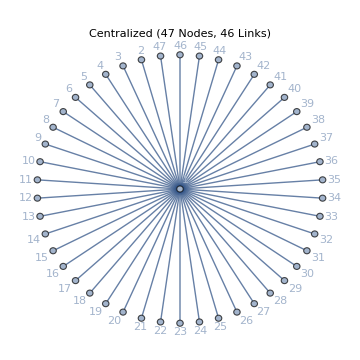

```mathematica
MSS=1500; 
C=1.22; 
mathisThroughput[RTT_?NumericQ,p_?NumericQ]:=(MSS/RTT)*(C/Sqrt[p]);
centralizedNetwork=StarGraph[47,ImageSize->Medium,VertexLabels->"Name",PlotLabel->"Centralized (47 Nodes, 46 Links)"]
```

Set::wrsym: Symbol C is Protected.

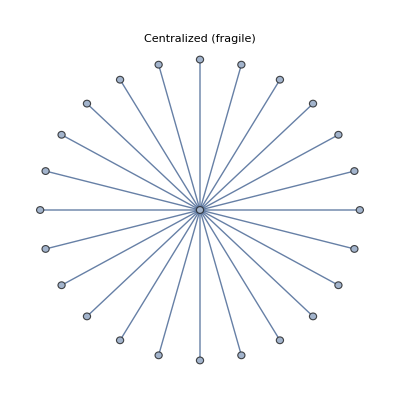
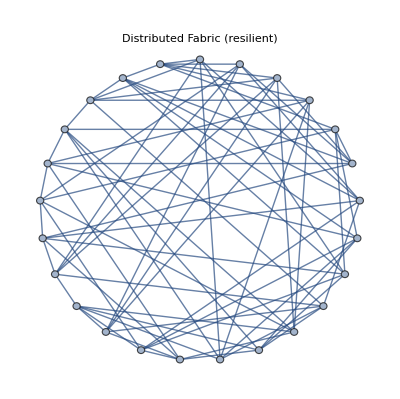
-Graphics- |  | -Graphics-

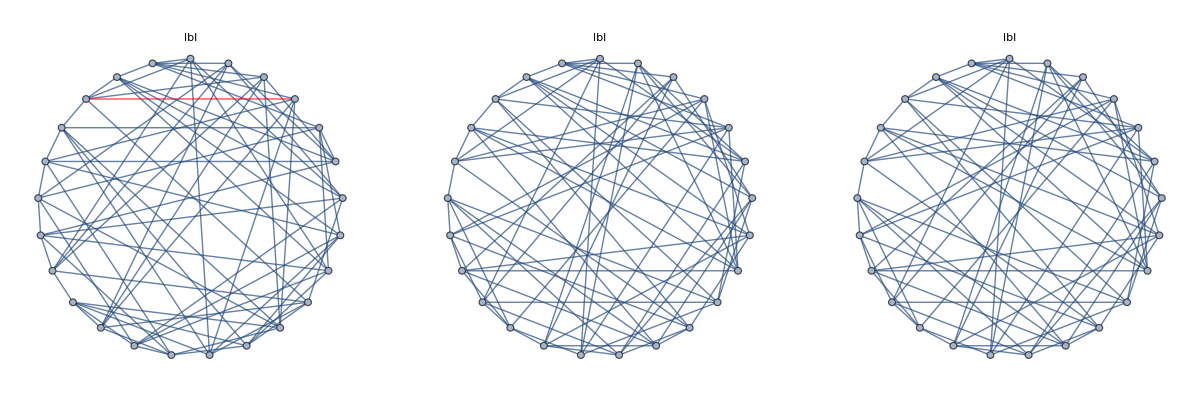

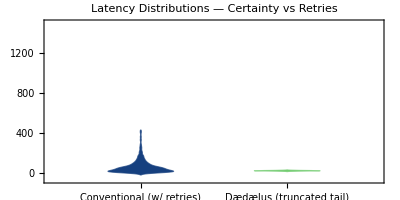

Reliability built **in-fabric**—not grafted on T-op—yields higher epistemic fidelity, bounded latency, and self-healing (didn't have to do anything) derivations of Wait Time.
That is the promise of a Dædælus-class network.

```mathematica
ClearAll["Global`*"];
SetOptions[{Plot,ListPlot,ListLinePlot,MatrixPlot,Graph},ImageSize->Large,PlotTheme->"Scientific",Frame->True,FrameStyle->Directive[GrayLevel[.35],12],LabelStyle->{FontFamily->"Avenir",13}];
palette=ColorData["BlueGreenYellow"];
MSSB=1500;     
MSBit=MSSB*8;      
C=1.22;      
mathis[τ_?NumericQ,p_?NumericQ]:=(MSBit/τ) (C/Sqrt[p]);   (*Can we graph the mathis?*)
centralized=StarGraph[25];
distributed=EdgeAdd[CycleGraph[25],Flatten@Table[{i<->Mod[i+3,25,1],i<->Mod[i+7,25,1]},{i,1,25}]];
decorate[g_,lbl_]:=SetProperty[g,{VertexLabels->Placed["Name",Tooltip],PlotLabel->Style[lbl,14,Bold]}];
Grid[{{decorate[centralized,"Centralized (fragile)"],Spacer[15],decorate[distributed,"Distributed Fabric (resilient)"]}},Frame->None]
resilience[g_Graph]:=<|"Vertex Connectivity"->VertexConnectivity[g],"Edge Connectivity"->EdgeConnectivity[g]|>;
Dataset[AssociationThread[{"Centralized","Distributed"},resilience/@{centralized,distributed}]]
simulateFailure[g_,e_]:=EdgeDelete[g,e];
localHeal[g_,{u_,v_}]:=Module[{n1=AdjacencyList[g,u],n2=AdjacencyList[g,v],shared,newEdges},shared=Intersection[n1,n2];
If[shared=!={},newEdges={u<->First[shared],First[shared]<->v};
EdgeAdd[g,newEdges],g]];
failedE=5<->8;
broken=simulateFailure[distributed,failedE];
healed=localHeal[broken,{5,8}];
GraphicsRow[HighlightGraph[#,Style[failedE,Thick,Red],GraphHighlightStyle->"Thick",PlotLabel->lbl]&@@@{{distributed,"1. Healthy Fabric"},{broken,"2. Link Failure"},{healed,"3. Healed via Local View"}}]
conventional:=RandomVariate[ExponentialDistribution[1/50]]+If[RandomReal[]<.1,RandomVariate[ExponentialDistribution[1/200]],0];
daedalus:=RandomVariate[NormalDistribution[20,3]];
latSamples=<|"Conventional (w/ retries)"->Table[conventional,2000],"Dædælus (truncated tail)"->Table[daedalus,2000]|>;
DistributionChart[Values@latSamples,ChartLabels->Keys@latSamples,ChartStyle->{palette[.15],palette[.75]},PlotLabel->Style["Latency Distributions — Certainty vs Retries",15,Bold],AspectRatio->1/2]
Style["Reliability built **in-fabric**—not grafted on T-op—yields higher epistemic fidelity, bounded latency, and self-healing (didn't have to do anything) derivations of Wait Time.\nThat is the promise of a Dædælus-class network.",14,Italic,Darker@Green]
```

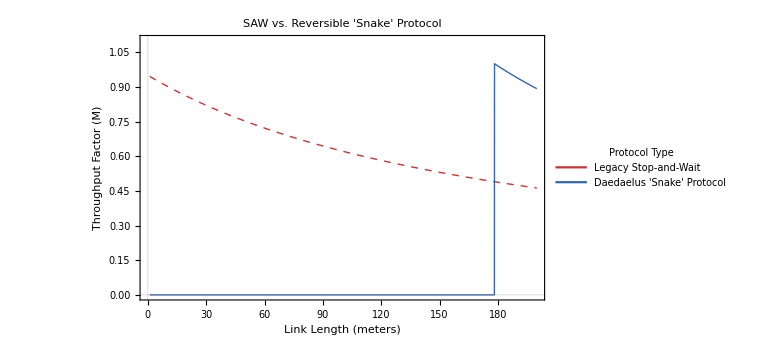

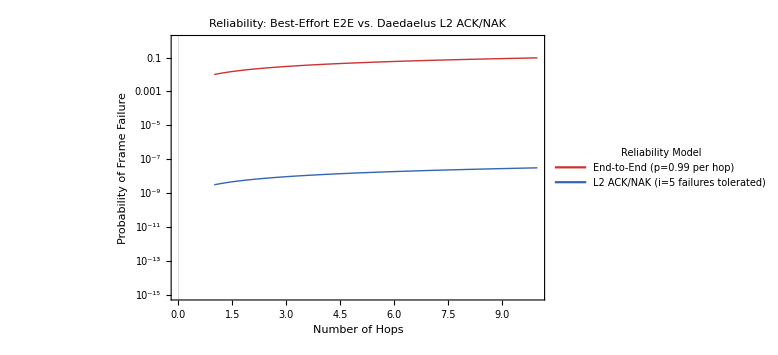

```mathematica
ClearAll["Global`*"];
SetOptions[{Plot,ListLinePlot,LogPlot,DiscretePlot},ImageSize->Large,PlotTheme->"Scientific",Frame->True,FrameStyle->GrayLevel[.3],LabelStyle->{FontFamily->"Avenir",14}];
$DaedalusBlue=RGBColor[0.2,0.4,0.7];
$LegacyRed=RGBColor[0.8,0.2,0.2];
sawDegradationFactor[C_?NumericQ,P_?NumericQ,A_?NumericQ,Tl_?NumericQ,Tr_?NumericQ]:=Module[{Tp=P/C,Ta=A/C},Tp/(Tp+Tl+2*Tr+Ta)];
snakeThroughputFactor[n_,C_?NumericQ,P_?NumericQ,Tl_?NumericQ,Tr_?NumericQ]:=Module[{Tp=P/C},(n*Tp)/(Tl+2*Tr)];
maxSnakes[C_?NumericQ,P_?NumericQ,Tl_?NumericQ,Tr_?NumericQ]:=Module[{Tp=P/C},Floor[(Tl+2*Tr)/Tp]];
Plot[{sawDegradationFactor[10*10^9,1500*8,64*8,(len/(3*10^8))*2,6*10^-9],snakeThroughputFactor[maxSnakes[10*10^9,1500*8,(len/(3*10^8))*2,6*10^-9],10*10^9,1500*8,(len/(3*10^8))*2,6*10^-9]},{len,1,200},PlotRange->{0,1.1},PerformanceGoal->"Quality",FrameLabel->{"Link Length (meters)","Throughput Factor (M)"},PlotLabel->Style["SAW vs. Reversible 'Snake' Protocol",18,Bold],PlotStyle->{{$LegacyRed,Dashed,Thick},{$DaedalusBlue,Thick}},PlotLegends->Placed[LineLegend[{$LegacyRed,$DaedalusBlue},{"Legacy Stop-and-Wait","Daedaelus 'Snake' Protocol"},LegendLabel->"Protocol Type"],{0.7,0.4}]]
bestEffortFailureProb[pHop_,numHops_]:=1-pHop^numHops;
ackNakFailureProb[pBiDirectional_,iFailures_,numHops_]:=Module[{q=1-pBiDirectional},1-(1-(q/(1-pBiDirectional*q^(iFailures-1)))^iFailures)^numHops];
LogPlot[{bestEffortFailureProb[0.99,h],ackNakFailureProb[0.99^2,5,h] },{h,1,10},PlotRange->{1*^-15,1},FrameLabel->{"Number of Hops","Probability of Frame Failure"},PlotLabel->Style["Reliability: Best-Effort E2E vs. Daedaelus L2 ACK/NAK",18,Bold],PlotLegends->Placed[LineLegend[{$LegacyRed,$DaedalusBlue},{"End-to-End (p=0.99 per hop)","L2 ACK/NAK (i=5 failures tolerated)"},LegendLabel->"Reliability Model"],{Left,Top}],PlotStyle->{{$LegacyRed,Thick},{$DaedalusBlue,Thick}}]
```

Q \ P | 4096 | 1024 | 512 | 48
1 | 1.0000 | 1.0000 | 1.0000 | 1.0000
2 | 0.9884 | 0.9552 | 0.9143 | 0.5000
3 | 0.9856 | 0.9446 | 0.8951 | 0.4444
4 | 0.9842 | 0.9396 | 0.8862 | 0.4219
5 | 0.9834 | 0.9367 | 0.8810 | 0.4096
10 | 0.9818 | 0.9310 | 0.8709 | 0.3874
32 | 0.9807 | 0.9272 | 0.8642 | 0.3737
64 | 0.9805 | 0.9263 | 0.8627 | 0.3708
128 | 0.9804 | 0.9259 | 0.8620 | 0.3693
256 | 0.9803 | 0.9257 | 0.8616 | 0.3686

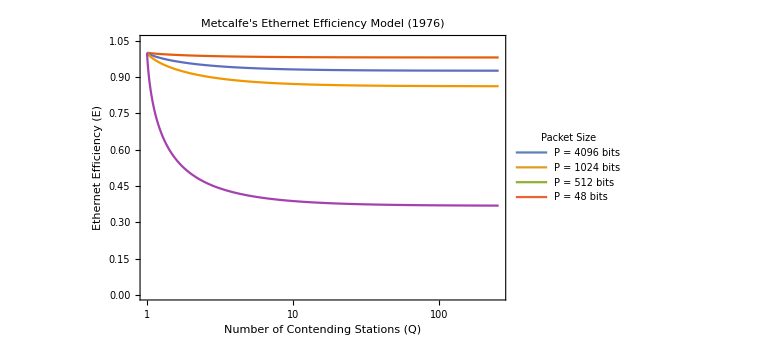

```mathematica
ClearAll["Global`*"];
SetOptions[{Plot,ListLinePlot,LogLinearPlot},ImageSize->Large,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Avenir",12}];
c=3*10^6;
t=16*10^-6; 
acquisitionProbabilityA[Q_?NumericQ]:=Module[{q=N[Q]},(1-1/q)^(q-1)];
meanWaitSlotsW[Q_?NumericQ]:=Module[{A=acquisitionProbabilityA[Q]},(1-A)/A];
ethernetEfficiencyE[Q_?NumericQ,P_?NumericQ]:=Module[{W,p=N[P]},If[Q==1,1.0,W=meanWaitSlotsW[Q];
(p/c)/((p/c)+W*t)]];
qValues={1,2,3,4,5,10,32,64,128,256};
pValues={4096,1024,512,48};
headerRow=Prepend[Style[#,Bold,14]&/@pValues,Style["Q \\ P",Bold,14]];
dataRows=Table[Prepend[NumberForm[#,{5,4}]&/@(ethernetEfficiencyE[q,#]&/@pValues),Style[q,Bold,14]],{q,qValues}];
tableData=Prepend[dataRows,headerRow];
Grid[tableData,Spacings->{2,1.5},Alignment->Center,Dividers->{2->True,2->True},ItemStyle->{"Text",14},Background->{None,{Lighter[Gray,.9],{White,Lighter[Gray,.95]}}}]
LogLinearPlot[Evaluate@Table[ethernetEfficiencyE[q,p],{p,pValues}],{q,1,256},PlotRange->{0,1.05},Frame->True,FrameLabel->{"Number of Contending Stations (Q)","Ethernet Efficiency (E)"},PlotLabel->Style["Metcalfe's Ethernet Efficiency Model (1976)",18,Bold],PlotLegends->Placed[LineLegend[ColorData[97,"ColorList"][[1;;Length[pValues]]],("P = "<>ToString[#]<>" bits")&/@pValues,LegendLabel->"Packet Size"],{Right,Center}],GridLines->{Automatic,{{1/E,GrayLevel[0.7]},{1.0,GrayLevel[0.7]}}},Epilog->{{Dashed,Gray,Text[Style["Slotted Aloha Limit (1/e) ≈ 0.3679",Italic,Gray],{30,1/E-0.05}]}}]
```

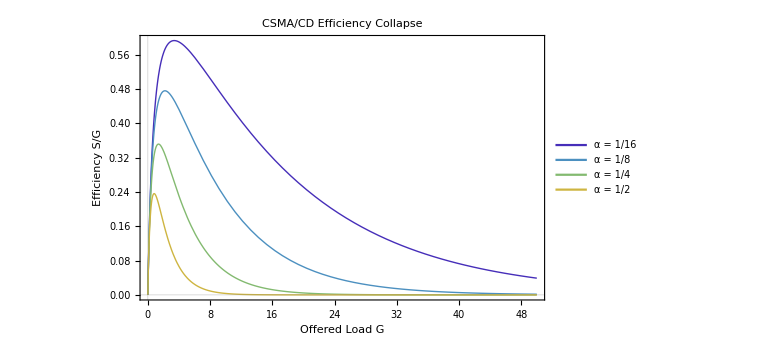

```mathematica
ClearAll["Global`*"];
SetOptions[{Plot},ImageSize->Large,PlotTheme->"Scientific",Frame->True,FrameStyle->GrayLevel[.35],LabelStyle->{FontFamily->"Avenir",14}];
palette=ColorData["Rainbow"];
csmaEfficiency[α_?NumericQ][g_]:=(g Exp[-α g])/(g (1+2 α)+Exp[-α g]);
αVals={1/16,1/8,1/4,1/2};
metcalfePlot=Plot[Evaluate@Table[csmaEfficiency[α][g],{α,αVals}],{g,0,50},PlotLegends->Placed[Style/@(Row[{"α = ",NumberForm[#,4]}]&/@αVals),Right],PlotStyle->Table[{palette[i],Thick},{i,0.1,0.9,0.2}],FrameLabel->{"Offered Load G","Efficiency S/G"},PlotLabel->Style["CSMA/CD Efficiency Collapse",18,Bold]];
metcalfePlot
```

```mathematica
ClearAll["Global`*"];
SetOptions[{Plot},ImageSize->Large,PlotTheme->"Scientific",Frame->True,FrameStyle->GrayLevel[.35],LabelStyle->{FontFamily->"Avenir",14}];
throughput[rtt_,p_,mss_:1460*8,c_:1.22]:=If[p==0,∞,mss/(c rtt Sqrt[p])];
Manipulate[Show[Plot[throughput[τ,p]/10^6,{τ,10^-5,0.1},PlotRange->{{0,0.1},{0,1000}},FrameLabel->{"RTT (s)","Throughput (Mbps)"},PlotLabel->Style["TCP Throughput vs. RTT and Packet Loss",18,Bold],PlotStyle->{Red,Thick},PlotPoints->50,MaxRecursion->3,Epilog->{Text[Style[Row[{"p = ",ScientificForm[p,2]}],14,Italic],{0.07,800}]}],Graphics[{Dashed,Gray,Line[{{τMark,0},{τMark,1000}}]}]],{{p,10^-4,"Packet Loss (p)"},10^-6,10^-2,Appearance->"Labeled"},{{τMark,0.002,"Mark RTT"},10^-5,0.05,Appearance->"Labeled"},TrackedSymbols:>{p,τMark}]
```

```mathematica
ClearAll[A,W,efficiency,qValues,pValues,peakCapacity,efficiencyTable,plot1,plot2];
A[1]=1;
A[Q_]:=N[(1-1/Q)^(Q-1)];
W[Q_]:=(1-A[Q])/A[Q];
efficiency[P_,Q_,peakCapacity_,T_]:=(P/peakCapacity)/((P/peakCapacity)+W[Q]*T);
qValues={1,2,3,4,5,10,32,64,128,256};
pValues={4096,1024,512,48};
Manipulate[efficiencyTable=Prepend[Table[Prepend[Table[NumberForm[N[efficiency[p,q,peakCapacity,T]],{5,4}],{p,pValues}],Style[q,Bold]],{q,qValues}],Prepend[pValues,Style["Q \\ P",Bold]]];
plot1=ListLinePlot[Table[Table[{q,efficiency[p,q,peakCapacity,T]},{q,qValues}],{p,pValues}],PlotTheme->"Detailed",PlotLegends->(ToString[#]<>" bits"&/@pValues),PlotLabel->"Efficiency vs. Number of Stations",AxesLabel->{"Number of Stations (Q)","Efficiency"},ImageSize->Large];
plot2=ListLinePlot[Table[Table[{p,efficiency[p,q,peakCapacity,T]},{p,pValues}],{q,Rest[qValues]} ],PlotTheme->"Detailed",PlotLegends->(ToString[#]<>" stations"&/@Rest[qValues]),PlotLabel->"Efficiency vs. Packet Size",AxesLabel->{"Packet Size (P)","Efficiency"},ImageSize->Large];
Column[{Row[{Control[{{peakCapacity,3,"Peak Capacity (megabits/sec)"},1,20,1,Appearance->"Labeled"}],Spacer[40],Control[{{T,16,"Slot Time (µs)"},2,50,2,Appearance->"Labeled"}]},Spacer[20]],Spacer[20],Labeled[TableForm[efficiencyTable,TableHeadings->{None,None},TableSpacing->{2,3}],"Efficiency",Top,LabelStyle->{Bold,GrayLevel[0.3]}],Spacer[20],Grid[{{plot1,plot2}}]},Alignment->Center],SaveDefinitions->True]
```